## Packages import and definitions

```mathematica
Get[NotebookDirectory[]<>"../QMB.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]]
```

```mathematica
ClearAll[Superoperator](*nuevo*)
Superoperator[t_,ψ0E_,eigVals_,eigVecs_,L_]:=
Module[{ψf,ρfSE(*SE final state*)},
Transpose[
ψf=StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[#],ψ0E],eigVals,eigVecs]&/@{{0},{1}};
ρfSE=Dyad[ψf[[#1]],ψf[[#2]]]&@@@Tuples[{1,2},2];
Transpose[Map[Flatten[MatrixPartialTrace[#,2,{2,2^(L-1)}]]&,ρfSE]]
]
]
```

```mathematica
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3]
```

## Setting parameters and global variables

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,1./2,ConstantArray[1.,L-1]}
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Chop[Eigensystem[H]];
]
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
```

```mathematica
Superoperator[10.,ψ0E,eigVals,eigVecs,L]
```

SparseArray[…]

```mathematica
AbsoluteTiming[superOp=Superoperator[10.,ψ0E,eigVals,eigVecs,L]]
```

{7.93979,SparseArray[<4194304>, {1048576, 4}]}

```mathematica
{eigenvalsChoi,eigenvecsChoi}=Eigensystem[Reshuffle[superOp]]
```

{{0.553157,0.518881,0.481124,0.446838},{{0.618598+0.1051 ⅈ,-0.30972+0.194194 ⅈ,-0.469347-0.258146 ⅈ,0.43096+0. ⅈ},{-0.0261649-0.0124788 ⅈ,0.0212703-0.141675 ⅈ,0.45809+0.326056 ⅈ,0.813927+0. ⅈ},{-0.51648+0.211214 ⅈ,-0.44625+0.684169 ⅈ,-0.0320653+0.109555 ⅈ,0.0915451+0. ⅈ},{-0.522874-0.14384 ⅈ,0.414617-0.0818837 ⅈ,-0.442685-0.433491 ⅈ,0.378703+0. ⅈ}}}

```mathematica
kraus=ArrayReshape[#,{2,2}]&/@eigenvecsChoi
```

{{{0.618598+0.1051 ⅈ,-0.30972+0.194194 ⅈ},{-0.469347-0.258146 ⅈ,0.43096+0. ⅈ}},{{-0.0261649-0.0124788 ⅈ,0.0212703-0.141675 ⅈ},{0.45809+0.326056 ⅈ,0.813927+0. ⅈ}},{{-0.51648+0.211214 ⅈ,-0.44625+0.684169 ⅈ},{-0.0320653+0.109555 ⅈ,0.0915451+0. ⅈ}},{{-0.522874-0.14384 ⅈ,0.414617-0.0818837 ⅈ},{-0.442685-0.433491 ⅈ,0.378703+0. ⅈ}}}

```mathematica
Table[kraus[[i+1]].Inverse[Pauli[i]],{i,0,3}]
```

{{{0.618598+0.1051 ⅈ,-0.30972+0.194194 ⅈ},{-0.469347-0.258146 ⅈ,0.43096+0. ⅈ}},{{0.0212703-0.141675 ⅈ,-0.0261649-0.0124788 ⅈ},{0.813927+0. ⅈ,0.45809+0.326056 ⅈ}},{{-0.684169-0.44625 ⅈ,0.211214+0.51648 ⅈ},{0.+0.0915451 ⅈ,0.109555+0.0320653 ⅈ}},{{-0.522874-0.14384 ⅈ,-0.414617+0.0818837 ⅈ},{-0.442685-0.433491 ⅈ,-0.378703+0. ⅈ}}}

```mathematica
Times@@%121
```

{{0.342182+0.0581367 ⅈ,-0.171324+0.10742 ⅈ,-0.259623-0.142795 ⅈ,0.238389+0. ⅈ},{-0.0135765-0.006475 ⅈ,0.0110368-0.0735123 ⅈ,0.237694+0.169184 ⅈ,0.422332+0. ⅈ},{-0.248491+0.10162 ⅈ,-0.214701+0.32917 ⅈ,-0.0154274+0.0527096 ⅈ,0.0440445+0. ⅈ},{-0.23364-0.0642732 ⅈ,0.185266-0.0365887 ⅈ,-0.197809-0.1937 ⅈ,0.169219+0. ⅈ}}

```mathematica
FullSimplify[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2]
```

{0.492059+0.0171156 x+0.00648548 y+0.00987586 z,(0.00435562+0.0136799 ⅈ)+(0.0408285+0.0219577 ⅈ) x-(0.0162195-0.00993043 ⅈ) y-(0.0119922+0.00580812 ⅈ) z,(0.00435562-0.0136799 ⅈ)+(0.0408285-0.0219577 ⅈ) x-(0.0162195+0.00993043 ⅈ) y-(0.0119922-0.00580812 ⅈ) z,0.507941-0.0171156 x-0.00648548 y-0.00987586 z}

```mathematica
{θ,ϕ}={RandomReal[{0,Pi}],RandomReal[{0,2Pi}]}
```

{1.50366,0.623916}

```mathematica
{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
```

{0.809769,0.582901,0.0670887}

```mathematica
superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2/.Rule@@@Transpose[{{x,y,z},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]
```

{0.484181+0. ⅈ,-0.00219251-0.00287134 ⅈ,-0.00219251+0.00287134 ⅈ,0.515819+0. ⅈ}

```mathematica
{Re[#2],-Im[#2],#1}&@@%
```

{-0.00219251,0.00287134,0.484181+0. ⅈ}

```mathematica
%//Norm
```

0.484195

```mathematica
{Re[#2],-Im[#2],Chop[#1]}&@@(superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2/.Rule@@@Transpose[{{x,y,z},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}])
```

{-0.0339366,-0.0134711,0.497307}

```mathematica
Table[{θ,ϕ}={RandomReal[{0,Pi}],RandomReal[{0,2Pi}]};
Graphics3D[{{Opacity[0.25],Sphere[]},{Opacity[0.25],Sphere[{0,0,0},0.5]},{PointSize[0.03],Point[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],Red,Point[{0,0,0}]},{PointSize[0.03],Blue,Point[{Re[#2],-Im[#2],Chop[#1]}&@@(superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2/.Rule@@@Transpose[{{x,y,z},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}])]}},ImageSize->330],
5]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Chaotic

```mathematica
colors={RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,0.5,0],RGBColor[1,0,1],RGBColor[0,1,1]};

Graphics3D[{{colors[[1]],PointSize[Large],Point[{1,0,0}]},{colors[[2]],PointSize[Large],Point[{-1,0,0}]},{colors[[3]],PointSize[Large],Point[{0,1,0}]},{colors[[4]],PointSize[Large],Point[{0,-1,0}]},{colors[[5]],PointSize[Large],Point[{0,0,1}]},{colors[[6]],PointSize[Large],Point[{0,0,-1}]}},Boxed->False,Axes->True,SphericalRegion->True]
```

-Graphics3D-

```mathematica
Graphics3D[{
{Red,PointSize[0.03],Point[{0,0,1}]},
{Green,PointSize[0.03],Point[{0,0,-1}]},
{Orange,PointSize[0.03],Point[{0,1,0}]},
{Cyan,PointSize[0.03],Point[{0,-1,0}]},
{Magenta,PointSize[0.03],Point[{1,0,0}]},
{Blue,PointSize[0.03],Point[{-1,0,0}]},
Flatten[Table[Point[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,Pi/30,Pi-Pi/30,Pi/30},{ϕ,0,2Pi,Pi/30}]]}]
```

-Graphics3D-

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=N[Chop[RandomChainProductState[L-1]]];
```

```mathematica
(*Choi eigenvalues*)
choiEigenvalues={};
```

### Plot bloch sphere

```mathematica
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.02],Point[f@@{0,0,1}]},
{Green,PointSize[0.02],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.02],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.02],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.02],Point[f@@{1,0,0}]},
{Pink,PointSize[0.02],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
```

-Graphics3D-

```mathematica
{t0,tf}={0,1};
```

```mathematica
figs=choiEigenvalues={};
```

```mathematica
AbsoluteTiming[(*cada iteración tarda ~7.4s en jungkook*)
Do[
superOp=Superoperator[t,ψ0E,eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs,
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
],
{t,t0,tf,.1}]
]
```

{78.34,Null}

```mathematica
7.4*Length[Range[0,3,0.1]]/60
```

3.82333

```mathematica
7.85*Length[Range[0,50,0.1]]/60
```

65.5475

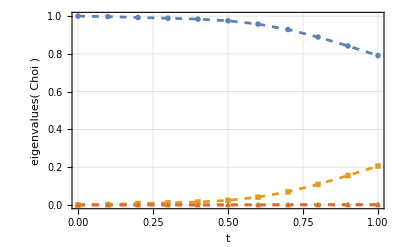

```mathematica
listPlot=ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"t","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->400]
```

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/animation.avi",Table[GraphicsRow[{Show[listPlot,Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[Round[t*10]+1]]},ImageSize->750],{t,0,tf,0.1}],"FrameRate"->2,"ImageSize"->{1920,1080}]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/animation.avi

## Integrable region

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}
```

{1.,2.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Chop[Eigensystem[H]];
]
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
(*SeedRandom[32371];(*regular1*)*)
SeedRandom[32971];(*regular2*)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
figs={};choiEigenvalues={};
```

```mathematica
{t0,tf}={10.1,25};
```

```mathematica
AbsoluteTiming[
Do[
superOp=Superoperator[t,ψ0E,eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs,
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.02],Point[f@@{0,0,1}]},
{Green,PointSize[0.02],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.02],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.02],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.02],Point[f@@{1,0,0}]},
{Pink,PointSize[0.02],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
],
{t,t0,tf,.1}]
]
```

{1259.85,Null}

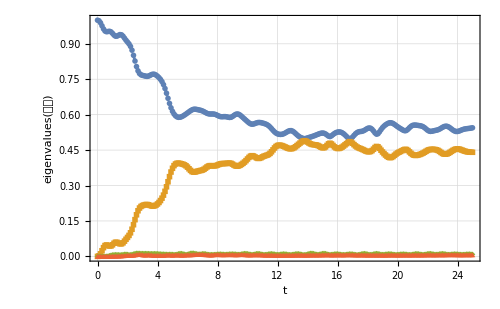

```mathematica
listPlot=ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues(𝒞𝒥)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]
```

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/bloch_sphere_and_CJ_eigenvalues_regular2.avi",Table[GraphicsRow[{Show[listPlot,Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[Round[t*10]+1]]},ImageSize->750],{t,0,tf,0.1}],"FrameRate"->2,"ImageSize"->{1920,1080}]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/bloch_sphere_and_CJ_eigenvalues_regular2.avi

## 3 different random initial states for the environment, integrable region (h_z=2.5, J=1), 0<=t<=50

```mathematica
tf=50.5
```

50.5

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=11(*number of spins*);
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]};

Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]

(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];

(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};listplots={};
Do[
AppendTo[figs,{}];choiEigenvalues={};
Do[
superOp=Superoperator[t,ψ0E[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];

AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]];
,{i,3}]
```

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/bloch_sphere_and_choi_eigenvalues_regular.avi",Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{700,950},Spacings->{-50,5},Alignment->{Center,Bottom}],{t,0,tf,0.1}],"ImageSize"->{700,950},"FrameRate"->4,"VideoCompression"->"MPEG4"];
```

```mathematica
grids=Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{700,950},Spacings->{-50,5},Alignment->{Center,Bottom}],{t,0,tf,0.1}];
```

```mathematica
grids[[1]]
```

-Graphics-

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/regular/frame"<>ToString[#]<>".png",grids[[#]],ImageSize->{700,900}]&/@Range[Length[grids]];
```

## 3 different random initial states for the environment, chaotic region (h_z=0.5, J=1), 0<=t<=50

```mathematica
tf=1
```

1

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]};

Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]

(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];

(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};listplots={};
Do[
AppendTo[figs,{}];choiEigenvalues={};
Do[
superOp=Superoperator[t,ψ0E[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];

AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]];
,{i,3}]
```

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/bloch_sphere_and_choi_eigenvalues_regular.avi",Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{700,950},Spacings->{-50,5},Alignment->{Center,Bottom}],{t,0,tf,0.1}],"ImageSize"->{700,950},"FrameRate"->4,"VideoCompression"->"MPEG4"];
```

```mathematica
grids=Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{700,950},Spacings->{-50,5},Alignment->{Center,Bottom}],{t,0,tf,0.1}];
```

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/chaotic/frame"<>ToString[#]<>".png",grids[[#]],ImageSize->{700,900}]&/@Range[Length[grids]];
```

```mathematica
Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{700,950},Spacings->{-50,5},Alignment->{Center,Bottom}],{t,tf,tf,0.1}]
```

{-Graphics-}